# Mетод на хордите

Задача: Да се реши уравнението 
(1. Да се намери броя на корените, 
2. Да се уточни най-малкия корен по метода на хордите (да се проверят условията за сходимост, да се определи началното приближение, да се извършат итерациите), 
3. Да се направи оценка на грешката)
		x^3+45cos x + 6x -76 = 0
Да се изчисли предварително броят на стъпките (итерациите) за достигане на точност 0.00001 за определения по време на локализацията интервал по метода на разполовяването и да се направи сравнение между двата метода.

## Графично представяне на функцията

### Дефиниция на функция

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
```

### Графика на функция

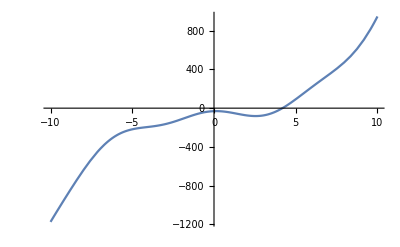

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Plot[function,{var,min,max}]
```

Plot::plln: Limiting value min in {var,min,max} is not a machine-sized real number.

Plot[function,{var,min,max}]

Извод: Уравнението има един корен.

## Локализация на корен

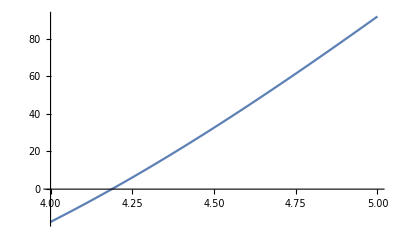

```mathematica
Plot[f[x],{x,4,5}]
```

```mathematica
f[4]
```

12+45 Cos[4]

```mathematica
f[4.]
```

-17.414

```mathematica
f[5.]
```

91.7648

Извод:
Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полиним и косинус). 
f(4) = -17.4... < 0
f(5) = 91.76... > 0
Функцията има различни знаци в двата края на разглеждания интервал [4; 5]. 
Следователно  в този интервал [4; 5] функцията има корен.

## Уточняване на корен по метода хордите

### да се проверят условията за сходимост

#### проверка знака на първата производна

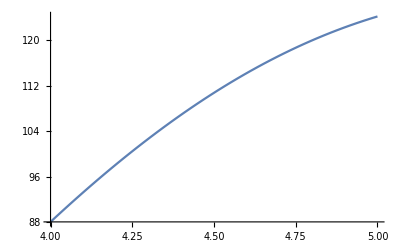

```mathematica
Plot[f'[x],{x,4,5}]
```

Извод: (1)Първата производна има стойности между 80 и 130. Следователно те са изцяло положителни. f’(x) > 0 за целия интервал [4; 5]

#### проверка знака на втората производна

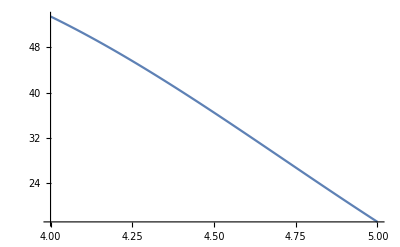

```mathematica
Plot[f''[x],{x,4,5}]
```

Извод: (2) Втората производна има стойности между 10 и 60. Следователно те са изцяло положителни. f’’(x) > 0 за целия интервал [4; 5]

От (1) и (2) следва, че са изпълнени условията на метода на хордите.

### да се определи началното приближение

Нужно е да е изпълнено условието f(x_0).f’’(x) < 0

В нашия случай f’’(x) >0. Следователно е нужно f(x_0) <0

```mathematica
f[4.]
```

-17.414

```mathematica
f[5.]
```

91.7648

```mathematica
x0 = 4.
```

4.

### да се извършат итерациите

BASIC VARIANT

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;b = 5.;
x0 = a; p = b;
For[
n = 1, n<=10, n++,
x1 = x0 - f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", x1, " f(x_n) = ", f[x1]];
x0 = x1
]
```

n = 1 x_n = 4.1595 f(x_n) = -2.70936

n = 2 x_n = 4.1836 f(x_n) = -0.376508

n = 3 x_n = 4.18694 f(x_n) = -0.0514479

n = 4 x_n = 4.1874 f(x_n) = -0.00701377

n = 5 x_n = 4.18746 f(x_n) = -0.000955868

n = 6 x_n = 4.18747 f(x_n) = -0.000130264

n = 7 x_n = 4.18747 f(x_n) = -0.0000177521

n = 8 x_n = 4.18747 f(x_n) = -2.41921×10^-6

n = 9 x_n = 4.18747 f(x_n) = -3.29684×10^-7

n = 10 x_n = 4.18747 f(x_n) = -4.49286×10^-8

### оценка на грешката

пресмятане на предварително зададените константи

M_1, m_1

```mathematica
Plot[Abs[f'[x]],{x,4,5}]
```

-Graphics-

по геометрични съображения:

```mathematica
M1 = Abs[f'[5.]]
m1= Abs[f'[4.]]
```

124.152

88.0561

```mathematica
P = (M1-m1)/m1
```

0.409915

f(p)

```mathematica
f[p]
```

91.7648

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;b = 5.;
x0 = a; p = b;
M1 = Abs[f'[5.]];
m1= Abs[f'[4.]];
P = (M1-m1)/m1;
Print["n = ", 0, " x_n = ", x0, " f(x_n) = ", f[x0]];
For[
n = 1, n<=10, n++,
x1 = x0 - f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = P*Abs[x1-x0]];
x0 = x1
]
```

n = 0 x_n = 4. f(x_n) = -17.414

n = 1 x_n = 4.1595 f(x_n) = -2.70936 ε_n = 0.0653812

n = 2 x_n = 4.1836 f(x_n) = -0.376508 ε_n = 0.00988064

n = 3 x_n = 4.18694 f(x_n) = -0.0514479 ε_n = 0.00136746

n = 4 x_n = 4.1874 f(x_n) = -0.00701377 ε_n = 0.000186752

n = 5 x_n = 4.18746 f(x_n) = -0.000955868 ε_n = 0.0000254575

n = 6 x_n = 4.18747 f(x_n) = -0.000130264 ε_n = 3.46942×10^-6

n = 7 x_n = 4.18747 f(x_n) = -0.0000177521 ε_n = 4.72806×10^-7

n = 8 x_n = 4.18747 f(x_n) = -2.41921×10^-6 ε_n = 6.44329×10^-8

n = 9 x_n = 4.18747 f(x_n) = -3.29684×10^-7 ε_n = 8.78076×10^-9

n = 10 x_n = 4.18747 f(x_n) = -4.49286×10^-8 ε_n = 1.19662×10^-9

за проверка на изчисленията на ръка:

```mathematica
4 --17.414/(-17.414-91.7648)*(4-5)
```

4.1595

цикъл при достигане на предварително зададена точност:

```mathematica
epszad = 0.00001;
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;b = 5.;
x0 = a; p = b;
M1 = Abs[f'[5.]];
m1= Abs[f'[4.]];
P = (M1-m1)/m1;
Print["n = ", 0, " x_n = ", x0, " f(x_n) = ", f[x0]];
eps = Infinity;
For[
n = 1, eps>epszad, n++,
x1 = x0 - f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = P*Abs[x1-x0]];
x0 = x1
]
```

n = 0 x_n = 4. f(x_n) = -17.414

n = 1 x_n = 4.1595 f(x_n) = -2.70936 ε_n = 0.0653812

n = 2 x_n = 4.1836 f(x_n) = -0.376508 ε_n = 0.00988064

n = 3 x_n = 4.18694 f(x_n) = -0.0514479 ε_n = 0.00136746

n = 4 x_n = 4.1874 f(x_n) = -0.00701377 ε_n = 0.000186752

n = 5 x_n = 4.18746 f(x_n) = -0.000955868 ε_n = 0.0000254575

n = 6 x_n = 4.18747 f(x_n) = -0.000130264 ε_n = 3.46942×10^-6

Извод: Необходими са 6 на брой итерации за достигане на точност 0.00001 по метода на хордите.

за метод на разполовяването:

```mathematica
Log2[(5-4)/0.00001]-1
```

15.6096

Извод: Необходими са 16 на брой итерации за достигане на точност 0.00001 по метода на разполовяването.

Извод: Методът на хордите е по-бърз отколкото методът на разполовяването.